```mathematica
{{"b","x"},{"a","y"}}
```

```mathematica
Sort@StringSplit["bayx",""]
```

{a,b,x,y}

## Recursions for gettingn the generating function

### Basic Functions for Recursion -- coalescence, migration, pop sorting, recombination

```mathematica
SortPop[config_]:=Module[{popList = Sort[#]&/@config},
Sort[ popList]
] (*we need this function to sort each population into a standard order, here assuming migration is symmetric*)
```

```mathematica
startConfig ={{{"a"},{"b"}},{}};
SortPop[startConfig]
```

{{},{{a},{b}}}

None

Empty

```mathematica
TakeAway::usage = "TakeAway[U,V]  gives the set U, minus elements V. Note that this is not the same as Complement[U,V] if U contains repeated elements. ";
```

```mathematica
TakeAway[U_List, {}] := U;
(*TakeAway[U_List,{{}}]:=If[MemberQ[U,{{}}],TakeAway[U,{{}}],U];*)
TakeAway[U_List, {v_}] := Drop[U, Cases[Position[U, v],{_Integer}]⟦1⟧] /; Complement[{v}, U] == {};
TakeAway[U_List, V_List] := TakeAway[TakeAway[U, Take[V, 1]], Drop[V, 1]] /; Complement[V, U] == {};
TakeAway[U_List, W__List, V_List] := TakeAway[TakeAway[U, W], V];
```

```mathematica
(*GetAnc takes a pair of individuals (with multple sites) and returns the common ancestor for coal event between them*)
GetAnc[pair_]:=Module[{charLists,stringLists},
charLists = MapThread[List,pair];
stringLists = StringJoin[#]&/@charLists;
charLists = StringSplit[#,""]&/@stringLists;
charLists = Sort[#]&/@charLists;
stringLists = StringJoin[#]&/@charLists;
(*MapThread[StringJoin,pair]*) (*creates the ancestor of two lineages chosen to coalesce*)
stringLists
];

(*CoalDeme takes a subpopulation "pop" and returns list of all possible configs resulting froma  coal event*)
CoalDeme[pop_]:=
Module[{pairList,ancList,newPopList},
If[Length[pop]< 2,Return[{}]]; (* no coal if fewer than two lineages in a deme*)
pairList = Subsets[pop,{2}]; (*pairs of lineages that can coal in this deme*)
ancList = GetAnc[#]&/@pairList; (*create ancestor from the pairs*)
newPopList =MapThread[TakeAway[pop,#1]~Join~{#2}&,{pairList,ancList}];(*new configs possible due to coal in this deme*)
Return[newPopList]
]
(*CoalPop takes a population with two demes and returns the list of all configs possible when coal occurs in one or the other demej*)
CoalPop[popList_]:=Module[{d1Coals,d2Coals},
d2Coals = {popList[[1]],#}&/@CoalDeme[popList[[2]]]; (*gets ways of coal in second deme*)
d2Coals = SortPop[#]&/@d2Coals;
d1Coals = {#,popList[[2]]}&/@CoalDeme[popList[[1]]]; (*gets ways of coal in first time*)
d1Coals = SortPop[#]&/@d1Coals;
Return[d1Coals~Join~d2Coals] (*return (sorted) populations*)
]
```

```mathematica
GetAnc[{{"z","y"},{"a","y"}}]
```

{az,yy}

```mathematica
(*MigratePop returns a list off all the ways a single lineage migrate (pastward)*) 
MigratePop[popList_]:=Module[
{oneToTwo,twoToOne},
oneToTwo = {TakeAway[popList[[1]],{#}],popList[[2]]~Join~{#}}&/@popList[[1]]; (*moves individuals from deme one to two*)
oneToTwo = SortPop[#]&/@oneToTwo;
twoToOne = {popList[[1]]~Join~{#},TakeAway[popList[[2]],{#}]}&/@popList[[2]];(*ways of moving ind from two to one*)
twoToOne = SortPop[#]&/@twoToOne;
Return[oneToTwo~Join~twoToOne] (*returns the (sorted) pops possible after mig*)
]
```

```mathematica
RecPop[popList_]:= Module[
{recombiningIndividuals,rls, recConfigs},
recombiningIndividuals = Cases[ Flatten[popList,1],{x_String,y_String}/;x≠ "" ∧ y≠ ""]; (* with two loci, only follow rec events involving ind with ancestral material at both sites. this returns list of individuals which may recombine*)
rls = #/.{x_,y_}:> ({x,y}:> Sequence[{x,""},{"",y}])&/@recombiningIndividuals; (*creates a list of rules, corresponding to each possible rec event*)
recConfigs = popList/.# &/@ rls; (*use these rules to update the population, removing the recomining individual and replaicng with two new lineages*)
recConfigs = SortPop[#]&/@recConfigs; (*sort the population configurations*)
Return[recConfigs] (*and return all possible configs after recombination event*)
]

RecRules[indLocs_,recInd_]:= #:> recInd&/@indLocs
RecPop2[popList_]:=Module[
{recIndividuals,positions,rls,partRules,newConfigs},
(*get a list of all the (unique) individuals which may undergo rec between the two loci*) 
recIndividuals = Cases[Flatten[popList,1],{x_String,y_String}/;x≠ "" ∧ y≠ ""];
recIndividuals = DeleteDuplicates[recIndividuals];
(*obtain the list of positions in pop corresponding to each (unique) lineage that may rec*)
positions = Position[popList,#]&/@recIndividuals;
(*for each uniqe rec lineage, this is the result of the recombination,creating two lieanges from one. *)
rls = {#}/.{x_,y_}:>{{x,""},{"",y}}&/@recIndividuals;
partRules = Flatten[MapThread[ RecRules[#1,#2]&,{positions,rls}],1];

newConfigs = ReplacePart[popList,#[[1]]->Sequence@@Sequence@@#[[2]]]&/@partRules;
newConfigs = SortPop[#]&/@newConfigs
];
```

```mathematica
CheckCoalStatus[pop_]:=Module[ (*this checks the status of the coalescent at each site*)
{byIndList,bySiteList,n,arr},
byIndList = Flatten[pop,1]; (*gets individuals across all demes into a list*)
bySiteList = Transpose[byIndList]; (*gets branch types present at each site*)
n  = Total[StringLength[#]&/@bySiteList[[1]]]; (*number of sampled individuals*)
(*Print[{byIndList,bySiteList,n}]*)
arr = (StringLength[#]&/@#)&/@bySiteList; (*number of lineages descending from each ancestor*)
Max[#]==n &/@arr (*returns list of True/False indicated whether site has coalesed (True) or not (False)*)
];
```

### Single Locus and One Deme NOTE: still pass the population as two demes, leaving one of them empty. migration is exluded building the recursion

```mathematica
GetSingleLocusOneDemeRecursion[currentConfig_,knownConfigs_]:=Module[
{n=Length[Flatten[currentConfig,1]],nextConfigsCoal,nextConfigsMig,allNextConfigs,gf,bl =ω[#]&/@Flatten[currentConfig]},

If[n==1,Return[{ϕ[currentConfig]==1,{},{}}]]; (*recursion stopping condition*)
nextConfigsCoal = CoalPop[currentConfig]; (*ways of coalescing current config*)
allNextConfigs = nextConfigsCoal;(*all possible new configs, used in recursion formula*)
allNextConfigs = Complement[allNextConfigs,knownConfigs]; (*configs not seen before that need a recursion defined in next step*)
gf = ϕ[currentConfig]== 1/(Length[nextConfigsCoal]+Total[bl])*(Total[ϕ[#]&/@nextConfigsCoal]); (* the single-step recursion equation for this config*)
Return[{gf,bl,allNextConfigs}]
]
```

```mathematica
GetSingleLocusOneDemeRecursion[ { { {"a"},{"b"},{"c"}},{}},{{ { {"a"},{"b"},{"c"}},{}} }]
```

{ϕ[{{{a},{b},{c}},{}}]==(ϕ[{{},{{a},{bc}}}]+ϕ[{{},{{ab},{c}}}]+ϕ[{{},{{ac},{b}}}])/(3+ω[a]+ω[b]+ω[c]),{ω[a],ω[b],ω[c]},{{{},{{a},{bc}}},{{},{{ab},{c}}},{{},{{ac},{b}}}}}

```mathematica
GetAllSingleLocusOneDemeRecursions[initialConfig_,knownConfigs_List]:=Module[
{currentConfigs = {SortPop[initialConfig]},recursionsSeen={},branchesSeen={},configsSeen=knownConfigs,gf,bList,newConfigs={},configList,wlitt}, 
(*{gf,bList,configList} = GetSingleLocusTwoDemeRecursion[currentConfigs⟦1⟧,configsSeen];
Return[{gf,bList,configList}];*)
(*current configs contains the pop configs which don't yet have a recursion step defined*)
While[True,
For[i=1,i≤ Length[currentConfigs],i++, (*for each of the current configs*)
{gf,bList,configList} = GetSingleLocusOneDemeRecursion[currentConfigs⟦i⟧,configsSeen]; (*get stingle-step gf recursion, the branches present during this step in coal, and the list of configs not seen before*)
(*Print[{gf,bList,configList}];*)
recursionsSeen = recursionsSeen~Join~{gf}; (* add each recursion to list of recursions*) 
branchesSeen = Union[bList,branchesSeen]; (*add any new branches observed in this step*)
configsSeen = Union[configsSeen,newConfigs];(* put the current config into list of configs seen*)
newConfigs = Union[newConfigs,configList];  (*add new configs accessible from current config to the list*)
];
(*Print[{wlitt,newConfigs}];*)
If[newConfigs=={},Break[]]; (*there are no new configurations accessible in the coal process, so have all recursions and break while loop*)
currentConfigs = newConfigs; (* otherwise, we continue by processing the new configs*)
newConfigs = {}; (*and clearin ghtis list for the next for loop*)

];
Return[{recursionsSeen,branchesSeen,configsSeen}] (*returns all the recursions observed, branches observed, and configurations observed during the process*)
];
```

```mathematica
GetAllSingleLocusOneDemeRecursions[ { { {"a"},{"b"}},{}},{ }]
```

{{ϕ[{{},{{a},{b}}}]==ϕ[{{},{{ab}}}]/(1+ω[a]+ω[b]),ϕ[{{},{{ab}}}]==1},{ω[a],ω[b]},{}}

```mathematica
tst1L1D= GetAllSingleLocusOneDemeRecursions[SortPop[{{{"a"},{"a"}},{}}],{}];
lhs1L1D = #[[1]]&/@tst1L1D[[1]];
omegas1L1D = tst1L1D[[2]];
recursionEquations1L1D = And[Evaluate[tst1L1D[[1]]]];
recursionsSolved1L1D = Solve[recursionEquations1L1D,lhs1L1D];
gf1L1D =  ϕ[SortPop[{{{"a"},{"a"}},{}}]]/.recursionsSolved1L1D;
gf1L1D/.{ ω[_]->θ/2}
```

{-1/(-1-θ)}

### Two Loci and One Deme NOTE: still pass the population as two demes, leaving one of them empty. migration is exluded building the recursion

```mathematica
GetTwoLociOneDemeRecursion[currentConfig_,knownConfigs_]:=
Module[
{n=Length[Flatten[currentConfig,1]],nextConfigsCoal,nextConfigsMig,nextConfigsRec,allNextConfigs,gf,bl =ω[#]&/@DeleteCases[Flatten[currentConfig],x_/;x==""]},
If[n==1,Return[{ϕ[currentConfig]==1,{},{}}]];
nextConfigsCoal = CoalPop[currentConfig];
nextConfigsRec = RecPop2[currentConfig];
allNextConfigs = nextConfigsCoal~Join~nextConfigsRec;
allNextConfigs = Complement[allNextConfigs,knownConfigs];
allNextConfigs = SortPop[#]&/@allNextConfigs;
gf = ϕ[currentConfig]== 1/(Length[nextConfigsCoal]+Length[nextConfigsRec]*R+Total[bl])*(Total[ϕ[#]&/@nextConfigsCoal]+R*Total[ϕ[#]&/@nextConfigsRec]);
Return[{gf,bl,allNextConfigs}]
]
```

```mathematica
GetTwoLociOneDemeRecursion[ { { {"a","x"},{"a",""},{"","x"}},{ }},{}]
```

{ϕ[{{{a,x},{a,},{,x}},{}}]==(ϕ[{{},{{,x},{aa,x}}}]+ϕ[{{},{{a,},{a,xx}}}]+ϕ[{{},{{a,x},{a,x}}}]+R ϕ[{{},{{,x},{,x},{a,},{a,}}}])/(3+R+2 ω[a]+2 ω[x]),{ω[a],ω[x],ω[a],ω[x]},{{{},{{,x},{aa,x}}},{{},{{a,},{a,xx}}},{{},{{a,x},{a,x}}},{{},{{,x},{,x},{a,},{a,}}}}}

```mathematica
GetAllTwoLociOneDemeRecursions[initialConfig_]:=Module[
{currentConfigs = {SortPop[initialConfig]},recursionsSeen={},branchesSeen={},configsSeen={SortPop[initialConfig]},thisConfig,coalStatus,gf,bList,newConfigs={},j,configList,wlitt,oneSiteConfig,oneSiteRecursions,oneSiteBranches,oneSiteConfigurations}, 

(*wlitt = 1;*)
While[True,
For[j=1,j≤ Length[currentConfigs],j++,
(*Print[j];*)
thisConfig = currentConfigs⟦j⟧;
coalStatus = CheckCoalStatus[thisConfig];
(*Print[{thisConfig,coalStatus}];*)
If[coalStatus == {False,True}, (*if the second site has coalesced*)
oneSiteConfig=thisConfig/.{{x_String,y_String}:>{x}}; (*create config for first site only*)
oneSiteConfig = DeleteCases[#,x_/;x=={""}]&/@oneSiteConfig; oneSiteConfig = SortPop[oneSiteConfig];(*create config for first site only*)
recursionsSeen = recursionsSeen~Join~{ϕ[thisConfig]== ϕ[oneSiteConfig]}; (* add mapping of the two-locus config to single-locus config for recursion*)
configsSeen  = Union[configsSeen,{thisConfig,oneSiteConfig}]; (*add one-site config to list of configs seen*)
{oneSiteRecursions,oneSiteBranches,oneSiteConfigurations} =  GetAllSingleLocusOneDemeRecursions[oneSiteConfig,configsSeen]; (*get all further recursions, branches , and configurations for this single-locus configuration*)
recursionsSeen = Union[recursionsSeen,oneSiteRecursions]; (*add the recursions, branches, and configs to our lists*)
branchesSeen = Union[branchesSeen,oneSiteBranches];
configsSeen = Union[configsSeen,oneSiteConfigurations];
];
If[coalStatus == {True,False}, (* similar to above, we get all recursions, branches, and configs seen when the first site coaleseces first*)
oneSiteConfig=thisConfig/.{{x_String,y_String}:>{y}};
oneSiteConfig = DeleteCases[#,x_/;x=={""}]&/@oneSiteConfig;
oneSiteConfig = SortPop[oneSiteConfig];
recursionsSeen = recursionsSeen~Join~{ϕ[thisConfig]== ϕ[oneSiteConfig]};
configsSeen  = Union[configsSeen,{thisConfig,oneSiteConfig}];
{oneSiteRecursions,oneSiteBranches,oneSiteConfigurations} =  GetAllSingleLocusOneDemeRecursions[oneSiteConfig,configsSeen];
recursionsSeen = Union[recursionsSeen,oneSiteRecursions];
branchesSeen = Union[branchesSeen,oneSiteBranches];
configsSeen = Union[configsSeen,oneSiteConfigurations];
];
If[(coalStatus == {True,True})∨(coalStatus == {False,False}), (*if both sites coalesce simultaneously to common ancestor or if neither site has coaleseced*)
{gf,bList,configList} = GetTwoLociOneDemeRecursion[thisConfig,configsSeen]; (*get this two locus recursion, branches present, and the new configurations that are accessible*)
recursionsSeen = recursionsSeen~Join~{gf}; (*add these to our list of  recursions, branches, and configs seen, and list of new configs that need a recursion defined*)
branchesSeen = Union[bList,branchesSeen];
configsSeen = Union[configsSeen,configList];
newConfigs = Union[configList,newConfigs];
];
];
(*newConfigs = Complement[newConfigs,configsSeen];*)
(*Print[newConfigs];*)
(*wlitt=wlitt+1;
If[wlitt≥20,Break[]];*)
If[newConfigs=={},Break[]]; (*stop the while loop when all accessible configurations in coalescent have a recursion defined*)
currentConfigs = newConfigs;
newConfigs = {};
];(*end of while loop def*)
Return[{recursionsSeen,branchesSeen}]
];
```

```mathematica
tst2L1D= GetAllTwoLociOneDemeRecursions[SortPop[{{{"a","x"},{"a","x"}},{}}]];
```

```mathematica
tst2L1D
```

{{ϕ[{{},{{aa}}}]==1,ϕ[{{},{{xx}}}]==1,ϕ[{{},{{aa,xx}}}]==1,ϕ[{{},{{a},{a}}}]==ϕ[{{},{{aa}}}]/(1+2 ω[a]),ϕ[{{},{{x},{x}}}]==ϕ[{{},{{xx}}}]/(1+2 ω[x]),ϕ[{{},{{,x},{aa,x}}}]==ϕ[{{},{{x},{x}}}],ϕ[{{},{{a,},{a,xx}}}]==ϕ[{{},{{a},{a}}}],ϕ[{{},{{a,x},{a,x}}}]==(ϕ[{{},{{aa,xx}}}]+2 R ϕ[{{},{{,x},{a,},{a,x}}}])/(1+2 R+2 ω[a]+2 ω[x]),ϕ[{{},{{,x},{,x},{aa,}}}]==ϕ[{{},{{x},{x}}}],ϕ[{{},{{,x},{a,},{a,x}}}]==(ϕ[{{},{{,x},{aa,x}}}]+ϕ[{{},{{a,},{a,xx}}}]+ϕ[{{},{{a,x},{a,x}}}]+R ϕ[{{},{{,x},{,x},{a,},{a,}}}])/(3+R+2 ω[a]+2 ω[x]),ϕ[{{},{{,xx},{a,},{a,}}}]==ϕ[{{},{{a},{a}}}],ϕ[{{},{{,x},{,x},{a,},{a,}}}]==(ϕ[{{},{{,x},{,x},{aa,}}}]+4 ϕ[{{},{{,x},{a,},{a,x}}}]+ϕ[{{},{{,xx},{a,},{a,}}}])/(6+2 ω[a]+2 ω[x])},{ω[a],ω[x]}}

```mathematica
tst2L1D= GetAllTwoLociOneDemeRecursions[SortPop[{{{"a","x"},{"a","x"}},{}}]];
lhs2L1D = #[[1]]&/@tst2L1D[[1]];
omegas2L1D = tst2L1D[[2]];
recursionEquations2L1D = And[Evaluate[tst2L1D[[1]]]];
recursionsSolved2L1D = Solve[recursionEquations2L1D,lhs2L1D];
gf2L1D =  ϕ[SortPop[{{{"a","x"},{"a","x"}},{}}]]/.recursionsSolved2L1D;
gf2L1D/.{R->ρ/2, ω[_]->θ/2}
```

{-(-9-27 θ-29 θ^2-13 θ^3-2 θ^4-(13 ρ)/2-(19 θ ρ)/2-(7 θ^2 ρ)/2-(θ^3 ρ)/2-ρ^2/2-(θ ρ^2)/2)/((1+θ)^2 (9+27 θ+20 θ^2+4 θ^3+(13 ρ)/2+(19 θ ρ)/2+3 θ^2 ρ+ρ^2/2+(θ ρ^2)/2))}

```mathematica
gf2L1D/.{R->0, ω[_]->θ/2}//FullSimplify
```

{1/(1+2 θ)}

### One Locus and Two Demes NOTE: must pass at least the starting configuration “current config” as a known config this is left in to be able to pass more configs that may already be known.

```mathematica
GetSingleLocusTwoDemeRecursion[currentConfig_,knownConfigs_]:=Module[
{n=Length[Flatten[currentConfig,1]],nextConfigsCoal,nextConfigsMig,allNextConfigs,gf,bl =ω[#]&/@Flatten[currentConfig]},

If[n==1,Return[{ϕ[currentConfig]==1,{},{}}]]; (*recursion stopping condition*)
nextConfigsCoal = CoalPop[currentConfig]; (*ways of coalescing current config*)
nextConfigsMig = MigratePop[currentConfig]; (*ways f migrating current config*)
allNextConfigs = nextConfigsCoal~Join~nextConfigsMig;(*all possible new configs, used in recursion formula*)
allNextConfigs = Complement[allNextConfigs,knownConfigs]; (*configs not seen before that need a recursion defined in next step*)
gf = ϕ[currentConfig]== 1/(Length[nextConfigsCoal]+Length[nextConfigsMig]*M+Total[bl])*(Total[ϕ[#]&/@nextConfigsCoal]+M*Total[ϕ[#]&/@nextConfigsMig]); (* the single-step recursion equation for this config*)
Return[{gf,bl,allNextConfigs}]
]
```

```mathematica
GetSingleLocusTwoDemeRecursion[{{{"a"}},{{"b"}}},{}]
```

{ϕ[{{{a}},{{b}}}]==(2 M ϕ[{{},{{a},{b}}}])/(2 M+ω[a]+ω[b]),{ω[a],ω[b]},{{{},{{a},{b}}}}}

```mathematica
(*NOTE: when you pass knownConfigs to GetAllSingleLocusTwoDemeRecursions, you also have to include the initial config. this makes it easier when refering to the single-locus recursion from the two-locus recursion and avoiding re-evaluating things*)

GetAllSingleLocusTwoDemeRecursions[initialConfig_,knownConfigs_List]:=Module[
{currentConfigs = {SortPop[initialConfig]},recursionsSeen={},branchesSeen={},configsSeen=knownConfigs,gf,bList,newConfigs={},configList,wlitt}, 
(*{gf,bList,configList} = GetSingleLocusTwoDemeRecursion[currentConfigs⟦1⟧,configsSeen];
Return[{gf,bList,configList}];*)
(*current configs contains the pop configs which don't yet have a recursion step defined*)
While[True,
For[i=1,i≤ Length[currentConfigs],i++, (*for each of the current configs*)
{gf,bList,configList} = GetSingleLocusTwoDemeRecursion[currentConfigs⟦i⟧,configsSeen]; (*get stingle-step gf recursion, the branches present during this step in coal, and the list of configs not seen before*)
(*Print[{gf,bList,configList}];*)
recursionsSeen = recursionsSeen~Join~{gf}; (* add each recursion to list of recursions*) 
branchesSeen = Union[bList,branchesSeen]; (*add any new branches observed in this step*)
configsSeen = Union[configsSeen,newConfigs];(* put the current config into list of configs seen*)
newConfigs = Union[newConfigs,configList];(*add new configs accessible from current config to the list*)

];
(*Print[{wlitt,newConfigs}];*)
If[newConfigs=={},Break[]]; (*there are no new configurations accessible in the coal process, so have all recursions and break while loop*)
currentConfigs = newConfigs; (* otherwise, we continue by processing the new configs*)
newConfigs = {}; (*and clearin ghtis list for the next for loop*)
];
Return[{recursionsSeen,branchesSeen,configsSeen}] (*returns all the recursions observed, branches observed, and configurations observed during the process*)
];
```

```mathematica
GetAllSingleLocusTwoDemeRecursions[SortPop[{{{"a"},{"b"}},{}}],{SortPop[{{{"a"},{"b"}},{}}]}]
```

{{ϕ[{{},{{a},{b}}}]==(ϕ[{{},{{ab}}}]+2 M ϕ[{{{a}},{{b}}}])/(1+2 M+ω[a]+ω[b]),ϕ[{{},{{ab}}}]==1,ϕ[{{{a}},{{b}}}]==(2 M ϕ[{{},{{a},{b}}}])/(2 M+ω[a]+ω[b])},{ω[a],ω[b]},{{{},{{a},{b}}}}}

```mathematica
tst1L2D= GetAllSingleLocusTwoDemeRecursions[SortPop[{{{"a"},{"b"}},{}}],{SortPop[{{{"a"},{"b"}},{}}]}];
lhs1L2D = #[[1]]&/@tst1L2D[[1]];
omegas1L2D = tst1L2D[[2]];
recursionEquations1L2D = And[Evaluate[tst1L2D[[1]]]]
recursionsSolved1L2D = Solve[recursionEquations1L2D,lhs1L2D]
gf1L2D =  ϕ[SortPop[{{{"a"},{"b"}},{}}]]/.recursionsSolved1L2D
gf1L2D/.{M->M/2, ω[_]->θ/2}
```

{ϕ[{{},{{a},{b}}}]==(ϕ[{{},{{ab}}}]+2 M ϕ[{{{a}},{{b}}}])/(1+2 M+ω[a]+ω[b]),ϕ[{{},{{ab}}}]==1,ϕ[{{{a}},{{b}}}]==(2 M ϕ[{{},{{a},{b}}}])/(2 M+ω[a]+ω[b])}

{{ϕ[{{},{{a},{b}}}]→-(-2 M-ω[a]-ω[b])/(2 M+ω[a]+4 M ω[a]+ω[a]^2+ω[b]+4 M ω[b]+2 ω[a] ω[b]+ω[b]^2),ϕ[{{},{{ab}}}]→1,ϕ[{{{a}},{{b}}}]→(2 M)/(2 M+ω[a]+4 M ω[a]+ω[a]^2+ω[b]+4 M ω[b]+2 ω[a] ω[b]+ω[b]^2)}}

{-(-2 M-ω[a]-ω[b])/(2 M+ω[a]+4 M ω[a]+ω[a]^2+ω[b]+4 M ω[b]+2 ω[a] ω[b]+ω[b]^2)}

{-(-M-θ)/(M+θ+2 M θ+θ^2)}

### Two Loci and Two Demes

```mathematica
(*NOTE: here we do NOT pass the "currentConfig" initially in the list of known configurations. this is needed for the single-locus two deme recursion only in this context*)
(*otherwise, the same as the single-locus recursion, only now including recombination events*)
GetTwoLociTwoDemeRecursion[currentConfig_,knownConfigs_]:=Module[
{n=Length[Flatten[currentConfig,1]],nextConfigsCoal,nextConfigsMig,nextConfigsRec,allNextConfigs,gf,bl =ω[#]&/@DeleteCases[Flatten[currentConfig],x_/;x==""]},
If[n==1,Return[{ϕ[currentConfig]==1,{},{}}]];
nextConfigsCoal = CoalPop[currentConfig];
nextConfigsMig = MigratePop[currentConfig];
nextConfigsRec = RecPop2[currentConfig];
allNextConfigs = nextConfigsCoal~Join~nextConfigsMig~Join~nextConfigsRec;
allNextConfigs = Complement[allNextConfigs,knownConfigs];
gf = ϕ[currentConfig]== 1/(Length[nextConfigsCoal]+Length[nextConfigsMig]*M+Length[nextConfigsRec]*R+Total[bl])*(Total[ϕ[#]&/@nextConfigsCoal]+M*Total[ϕ[#]&/@nextConfigsMig]+R*Total[ϕ[#]&/@nextConfigsRec]);
Return[{gf,bl,allNextConfigs}]
]
```

```mathematica
GetTwoLociTwoDemeRecursion[{{},{{"a","x"},{"b","y"}}},{}]
```

{ϕ[{{},{{a,x},{b,y}}}]==(ϕ[{{},{{ab,xy}}}]+R (ϕ[{{},{{,x},{a,},{b,y}}}]+ϕ[{{},{{,y},{a,x},{b,}}}])+2 M ϕ[{{{a,x}},{{b,y}}}])/(1+2 M+2 R+ω[a]+ω[b]+ω[x]+ω[y]),{ω[a],ω[x],ω[b],ω[y]},{{{},{{ab,xy}}},{{},{{,x},{a,},{b,y}}},{{},{{,y},{a,x},{b,}}},{{{a,x}},{{b,y}}}}}

```mathematica
GetAllTwoLociTwoDemeRecursions[initialConfig_]:=Module[
{currentConfigs = {SortPop[initialConfig]},recursionsSeen={},branchesSeen={},configsSeen={initialConfig},thisConfig,coalStatus,gf,bList,newConfigs={},configList,wlitt,oneSiteConfig,oneSiteRecursions,oneSiteBranches,oneSiteConfigurations}, 


While[True,
For[j=1,j≤ Length[currentConfigs],j++,
(*Print[j];*)
thisConfig = currentConfigs⟦j⟧;
coalStatus = CheckCoalStatus[thisConfig];
(*Print[{thisConfig,coalStatus}];*)
If[coalStatus == {False,True}, (*if the second site has coalesced*)
oneSiteConfig=thisConfig/.{{x_String,y_String}:>{x}}; (*create config for first site only*)
oneSiteConfig = DeleteCases[#,x_/;x=={""}]&/@oneSiteConfig; 
oneSiteConfig = SortPop[oneSiteConfig];(*create config for first site only*)
recursionsSeen = recursionsSeen~Join~{ϕ[thisConfig]== ϕ[oneSiteConfig]}; (* add mapping of the two-locus config to single-locus config for recursion*)
configsSeen  = Union[configsSeen,{thisConfig,oneSiteConfig}]; (*add one-site config to list of configs seen*)
{oneSiteRecursions,oneSiteBranches,oneSiteConfigurations} =  GetAllSingleLocusTwoDemeRecursions[oneSiteConfig,configsSeen]; (*get all further recursions, branches , and configurations for this single-locus configuration*)
recursionsSeen = Union[recursionsSeen,oneSiteRecursions]; (*add the recursions, branches, and configs to our lists*)
branchesSeen = Union[branchesSeen,oneSiteBranches];
configsSeen = Union[configsSeen,oneSiteConfigurations];
];
If[coalStatus == {True,False}, (* similar to above, we get all recursions, branches, and configs seen when the first site coaleseces first*)
oneSiteConfig=thisConfig/.{{x_String,y_String}:>{y}};
oneSiteConfig = DeleteCases[#,x_/;x=={""}]&/@oneSiteConfig;
oneSiteConfig = SortPop[oneSiteConfig];
recursionsSeen = recursionsSeen~Join~{ϕ[thisConfig]== ϕ[oneSiteConfig]};
configsSeen  = Union[configsSeen,{thisConfig,oneSiteConfig}];
{oneSiteRecursions,oneSiteBranches,oneSiteConfigurations} =  GetAllSingleLocusTwoDemeRecursions[oneSiteConfig,configsSeen];
recursionsSeen = Union[recursionsSeen,oneSiteRecursions];
branchesSeen = Union[branchesSeen,oneSiteBranches];
configsSeen = Union[configsSeen,oneSiteConfigurations];
];
If[(coalStatus == {True,True})∨(coalStatus == {False,False}), (*if both sites coalesce simultaneously to common ancestor or if neither site has coaleseced*)
{gf,bList,configList} = GetTwoLociTwoDemeRecursion[thisConfig,configsSeen]; (*get this two locus recursion, branches present, and the new configurations that are accessible*)
recursionsSeen = recursionsSeen~Join~{gf}; (*add these to our list of  recursions, branches, and configs seen, and list of new configs that need a recursion defined*)
branchesSeen = Union[bList,branchesSeen];
configsSeen = Union[configsSeen,configList];
newConfigs = Union[configList,newConfigs];
];
];
(*Print[newConfigs];*)
If[newConfigs=={},Break[]]; (*stop the while loop when all accessible configurations in coalescent have a recursion defined*)
currentConfigs = newConfigs;
newConfigs = {};
];(*end of while loop def*)
Return[{recursionsSeen,branchesSeen}]
];
```

```mathematica
GetAllSingleLocusTwoDemeRecursions[SortPop[{{{"a"},{"b"}},{}}],{SortPop[{{{"a"},{"b"}},{}}]}]
```

{{ϕ[{{},{{a},{b}}}]==(ϕ[{{},{{ab}}}]+2 M ϕ[{{{a}},{{b}}}])/(1+2 M+ω[a]+ω[b]),ϕ[{{},{{ab}}}]==1,ϕ[{{{a}},{{b}}}]==(2 M ϕ[{{},{{a},{b}}}])/(2 M+ω[a]+ω[b])},{ω[a],ω[b]},{{{},{{a},{b}}}}}

## Results

```mathematica
GetAllTwoLociTwoDemeRecursions[SortPop[{{{"a","x"},{"a","x"}},{}}]]
```

{{ϕ[{{},{{aa}}}]==1,ϕ[{{},{{xx}}}]==1,ϕ[{{},{{aa,xx}}}]==1,ϕ[{{},{{a},{a}}}]==(ϕ[{{},{{aa}}}]+2 M ϕ[{{{a}},{{a}}}])/(1+2 M+2 ω[a]),ϕ[{{},{{x},{x}}}]==(ϕ[{{},{{xx}}}]+2 M ϕ[{{{x}},{{x}}}])/(1+2 M+2 ω[x]),ϕ[{{},{{,x},{aa,x}}}]==ϕ[{{},{{x},{x}}}],ϕ[{{},{{a,},{a,xx}}}]==ϕ[{{},{{a},{a}}}],ϕ[{{},{{a,x},{a,x}}}]==(ϕ[{{},{{aa,xx}}}]+2 R ϕ[{{},{{,x},{,x},{a,},{a,}}}]+2 M ϕ[{{{a,x}},{{a,x}}}])/(1+2 M+2 R+2 ω[a]+2 ω[x]),ϕ[{{},{{,x},{,x},{aa,}}}]==ϕ[{{},{{x},{x}}}],ϕ[{{},{{,x},{a,},{a,x}}}]==1/(3+3 M+R+2 ω[a]+2 ω[x])(ϕ[{{},{{,x},{aa,x}}}]+ϕ[{{},{{a,},{a,xx}}}]+ϕ[{{},{{a,x},{a,x}}}]+R ϕ[{{},{{,x},{,x},{a,},{a,}}}]+M (ϕ[{{{,x}},{{a,},{a,x}}}]+ϕ[{{{a,}},{{,x},{a,x}}}]+ϕ[{{{a,x}},{{,x},{a,}}}])),ϕ[{{},{{,xx},{a,},{a,}}}]==ϕ[{{},{{a},{a}}}],ϕ[{{},{{,x},{,x},{a,},{a,}}}]==1/(6+4 M+2 ω[a]+2 ω[x])(ϕ[{{},{{,x},{,x},{aa,}}}]+4 ϕ[{{},{{,x},{a,},{a,x}}}]+ϕ[{{},{{,xx},{a,},{a,}}}]+M (2 ϕ[{{{,x}},{{,x},{a,},{a,}}}]+2 ϕ[{{{a,}},{{,x},{,x},{a,}}}])),ϕ[{{{a}},{{a}}}]==(2 M ϕ[{{},{{a},{a}}}])/(2 M+2 ω[a]),ϕ[{{{x}},{{x}}}]==(2 M ϕ[{{},{{x},{x}}}])/(2 M+2 ω[x]),ϕ[{{{,x}},{{aa,x}}}]==ϕ[{{{x}},{{x}}}],ϕ[{{{,x}},{{,x},{aa,}}}]==ϕ[{{{x}},{{x}}}],ϕ[{{{,x}},{{a,},{a,x}}}]==1/(1+3 M+R+2 ω[a]+2 ω[x])(ϕ[{{{,x}},{{aa,x}}}]+R ϕ[{{{,x}},{{,x},{a,},{a,}}}]+M (ϕ[{{},{{,x},{a,},{a,x}}}]+ϕ[{{{a,}},{{,x},{a,x}}}]+ϕ[{{{a,x}},{{,x},{a,}}}])),ϕ[{{{,x}},{{,x},{a,},{a,}}}]==1/(3+4 M+2 ω[a]+2 ω[x])(ϕ[{{{,x}},{{,x},{aa,}}}]+2 ϕ[{{{,x}},{{a,},{a,x}}}]+M (ϕ[{{},{{,x},{,x},{a,},{a,}}}]+ϕ[{{{,x},{,x}},{{a,},{a,}}}]+2 ϕ[{{{,x},{a,}},{{,x},{a,}}}])),ϕ[{{{,xx}},{{a,},{a,}}}]==ϕ[{{},{{a},{a}}}],ϕ[{{{a,}},{{a,xx}}}]==ϕ[{{{a}},{{a}}}],ϕ[{{{a,}},{{,x},{a,x}}}]==1/(1+3 M+R+2 ω[a]+2 ω[x])(ϕ[{{{a,}},{{a,xx}}}]+R ϕ[{{{a,}},{{,x},{,x},{a,}}}]+M (ϕ[{{},{{,x},{a,},{a,x}}}]+ϕ[{{{,x}},{{a,},{a,x}}}]+ϕ[{{{a,x}},{{,x},{a,}}}])),ϕ[{{{a,}},{{,xx},{a,}}}]==ϕ[{{{a}},{{a}}}],ϕ[{{{a,}},{{,x},{,x},{a,}}}]==1/(3+4 M+2 ω[a]+2 ω[x])(2 ϕ[{{{a,}},{{,x},{a,x}}}]+ϕ[{{{a,}},{{,xx},{a,}}}]+M (ϕ[{{},{{,x},{,x},{a,},{a,}}}]+ϕ[{{{,x},{,x}},{{a,},{a,}}}]+2 ϕ[{{{,x},{a,}},{{,x},{a,}}}])),ϕ[{{{a,x}},{{a,x}}}]==(2 M ϕ[{{},{{a,x},{a,x}}}]+2 R ϕ[{{{,x},{a,}},{{,x},{a,}}}])/(2 M+2 R+2 ω[a]+2 ω[x]),ϕ[{{{a,x}},{{,x},{a,}}}]==1/(1+3 M+R+2 ω[a]+2 ω[x])(M (ϕ[{{},{{,x},{a,},{a,x}}}]+ϕ[{{{,x}},{{a,},{a,x}}}]+ϕ[{{{a,}},{{,x},{a,x}}}])+ϕ[{{{a,x}},{{a,x}}}]+R ϕ[{{{,x},{a,}},{{,x},{a,}}}]),ϕ[{{{aa,}},{{,x},{,x}}}]==ϕ[{{},{{x},{x}}}],ϕ[{{{,x},{,x}},{{a,},{a,}}}]==(ϕ[{{{,xx}},{{a,},{a,}}}]+M (2 ϕ[{{{,x}},{{,x},{a,},{a,}}}]+2 ϕ[{{{a,}},{{,x},{,x},{a,}}}])+ϕ[{{{aa,}},{{,x},{,x}}}])/(2+4 M+2 ω[a]+2 ω[x]),ϕ[{{{,x},{a,}},{{,x},{a,}}}]==(M (2 ϕ[{{{,x}},{{,x},{a,},{a,}}}]+2 ϕ[{{{a,}},{{,x},{,x},{a,}}}])+2 ϕ[{{{a,x}},{{,x},{a,}}}])/(2+4 M+2 ω[a]+2 ω[x])},{ω[a],ω[x]}}

Obtain the recursion and solve to obtain the generating function for the history of our sample.

```mathematica
tst2L2D= GetAllTwoLociTwoDemeRecursions[SortPop[{{{"a","x"},{"a","x"}},{}}]];
lhs2L2D = #[[1]]&/@tst2L2D[[1]];  (*get the functions for which we are trying to solve, i.e. the left hand side of each recursion*)
omegas2L2D = tst2L2D[[2]]; (*get the list of omega variables observed across all recursion steps*)
recursionEquations2L2D = And[Evaluate[tst2L2D[[1]]]]; (*input prepared for the solver*)
recursionsSolved2L2D = Solve[recursionEquations2L2D,lhs2L2D]; (*solve recursions *)
gf2L2D =  ϕ[SortPop[{{{"a","x"},{"a","x"}},{}}]]/.recursionsSolved2L2D; (*obtain gf for the coal history of our sample*)
```

substitute per-lienage migration rates and recombination rates. Rename omega variables to represent sites one and two.

```mathematica
gfMain = gf2L2D/.{M->μ/2,R->ρ/2,ω["a"]->ω1,ω["x"]->ω2}; (*substitue per-lineage rates of migration and recombination in the coal model and rename the branch variables to correspond to locus one and two*)
```

Calculate the two-locus het measures H0, H1, and H2 using the generating function

```mathematica
(*the probability that no mutation occurs at either site in the genealogy*)H0 = gfMain/.{ω1->θ/2,ω2->θ/2}; 

(*the probability that a mutation occurs at one but not both sites*)
(*with infinite sites, multiple mutations still means heterozygous at that site*)
(*a site can only be homozygous if no mutation occurs*)
(*Therefore, this is obtained as the marginal probaiblity of seeing no mutation at one site,  gfMain/.{ω1->θ/2,ω2->0}, minus the probability of seeing homozygosity at both sites*)
H1 =(( gfMain/.{ω1->θ/2,ω2->0}) -( gfMain/.{ω1->θ/2,ω2->θ/2})) + (( gfMain/.{ω1->0,ω2->θ/2}) - (gfMain/.{ω1->θ/2,ω2->θ/2}));
(*and H2 is calculated simply as*)
H2 = 1 - H0-H1;
```

These are the expected probabilites for the single-deme two-locus heterozygosity measures

```mathematica
sdh0 = 1/(1+θ)^2 + δ (1/(1+θ )* θ/(1+θ )) /.{δ-> (θ (18+4 θ^2+ρ+θ (18+ρ)))/(18+8 θ^3+13 ρ+ρ^2+θ^2 (40+6 ρ)+θ (54+19 ρ+ρ^2))}
sdh2 =( θ/(1+θ))^2 + δ (1/(1+θ )* θ/(1+θ )) /.{δ-> (θ (18+4 θ^2+ρ+θ (18+ρ)))/(18+8 θ^3+13 ρ+ρ^2+θ^2 (40+6 ρ)+θ (54+19 ρ+ρ^2))}
sdh1 = 1 - sdh0 -sdh2
{sdh0,sdh1,sdh2}/.{θ->0.0071,ρ->0.0017}
```

1/(1+θ)^2+(θ^2 (18+4 θ^2+ρ+θ (18+ρ)))/((1+θ)^2 (18+8 θ^3+13 ρ+ρ^2+θ^2 (40+6 ρ)+θ (54+19 ρ+ρ^2)))

θ^2/(1+θ)^2+(θ^2 (18+4 θ^2+ρ+θ (18+ρ)))/((1+θ)^2 (18+8 θ^3+13 ρ+ρ^2+θ^2 (40+6 ρ)+θ (54+19 ρ+ρ^2)))

1-1/(1+θ)^2-θ^2/(1+θ)^2-(2 θ^2 (18+4 θ^2+ρ+θ (18+ρ)))/((1+θ)^2 (18+8 θ^3+13 ρ+ρ^2+θ^2 (40+6 ρ)+θ (54+19 ρ+ρ^2)))

{0.985999,0.0139026,0.0000986527}

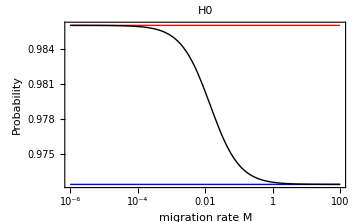

```mathematica
toPloth0 = { sdh0 /. {θ->0.0071, ρ->0.0017},sdh0 /. {θ->0.0071*2, ρ->0.0017*2},H0/.{θ->0.0071, ρ->0.0017}};
LogLinearPlot[toPloth0,
{μ,10^-6,10^2},
PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Black}},
PlotRange->Full,
PlotLabel->"H0",
Frame->True,FrameStyle->Directive[14,Bold,Thick,Black],FrameLabel->{"migration rate M","Probability"},
ImageSize->Medium]
```

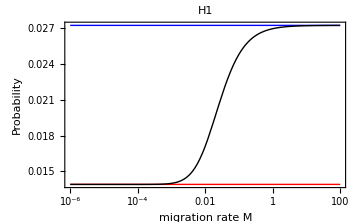

```mathematica
toPloth1 = { sdh1 /. {θ->0.0071, ρ->0.0017},sdh1 /. {θ->0.0071*2, ρ->0.0017*2},H1/.{θ->0.0071, ρ->0.0017}};
LogLinearPlot[toPloth1,
{μ,10^-6,10^2},
PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Black}},
PlotRange->Full,
PlotLabel->"H1",
Frame->True,FrameStyle->Directive[14,Bold,Thick,Black],FrameLabel->{"migration rate M","Probability"},
ImageSize->Medium]
```

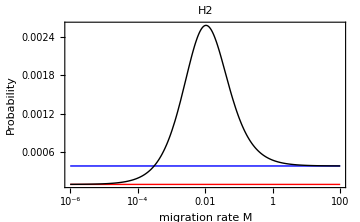

```mathematica
toPloth2 = { sdh2 /. {θ->0.0071, ρ->0.0017},sdh2 /. {θ->0.0071*2, ρ->0.0017*2},H2/.{θ->0.0071, ρ->0.0017}};
LogLinearPlot[toPloth2,
{μ,10^-6,10^2},
PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Black}},
PlotRange->Full,
PlotLabel->"H2",
Frame->True,FrameStyle->Directive[14,Bold,Thick,Black],FrameLabel->{"migration rate M","Probability"},ImageSize->Medium]
```